In the following explanations:
w_t - wages at time t
r_t - return on capital at time t
C_t - consumption at time t
L_t - labour at time t
K_t- capital at time t
I_t - investment at time t
Y_t  - output at time t
(K^f)_t - firms choice of capital at time t
(L^f)_t - firms choice of labour at time t
Π_t - profits at time t
(Π^f)_t - firm profits at time t
δ - depreciation of capital
A - level of technology
α - Capital income share

```mathematica
Question 3
```

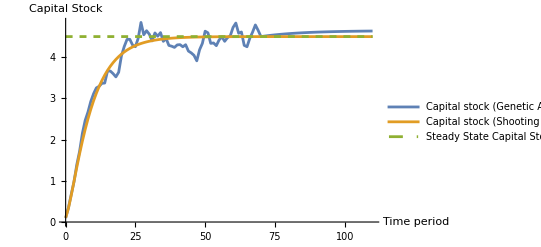

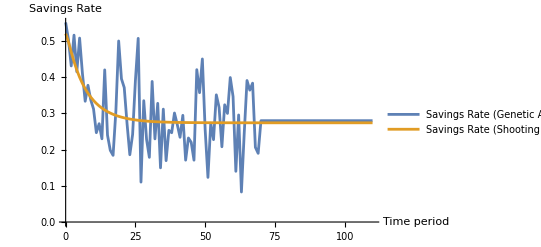

```mathematica
(*From question 1, we derived an expression for the steady state of capital.Substituting in our parameters, we can analytically find the steady state.*)
kss=A (α/(1/β-1+δ))^(1/(1-α));

(*To create a graph where we plot both capital stock from the genetic and shooting star algorithms, we need to extend the shooting star capital stock to be the same length as the genetic algorithm. The genetic algorithm is longer because we required additional periods for capital to reach its steady state.*)
capitalShootingExtended=

(*We join our shooting star capital series to a constant array with enough entries to accommodate the missing values. We know that at T the shooting star algorithm has reached the steady state. Therefore,the constant array is made up of the final value in the shooting star capital series (the steady-state value).*)
Join[capitalShooting,ConstantArray[Last[capitalShooting],Length[capitalstockGenetic]-Length[capitalShooting]]];

(*We plot a graph with three sets of data: both capital series and a horizontal line at the analytically calculated steady-state.*)
ListLinePlot[

(*Mathematica indexes lists from 1, but our periods start from T=0. We use 'Table' to subtract 1 from each index,ensuring our graph accurately plots the data.*)
{Table[{t,capitalstockGenetic[[t+1]]},{t,0,Length[capitalstockGenetic]-1}],
Table[{t,capitalShootingExtended[[t+1]]},{t,0,Length[capitalShootingExtended]-1}],

(*We plot a horizontal line as a dataset,where capital remains constant at the steady state for every period. This method allows us to label the horizontal line in the legend for clarity.*)
Table[{t,kss},{t,0,Length[capitalstockGenetic]-1}]},

(*Graph settings, including range, axis labels, and legend*)
Joined->True,PlotRange->All,AxesLabel->{"Time period","Capital Stock"},PlotLegends->Placed[{"Capital stock (Genetic Algorithm)","Capital stock (Shooting star Algorithm)","Steady State Capital Stock (kss)"},Below],PlotStyle->{Automatic,Automatic,Dashed}]

(*Similar to when plotting capital stock, we need to extend the shooting star algorithm's savings rate to the same length as the genetic algorithm.*)
savingShootingExtended=Join[savingShooting,ConstantArray[Last[savingShooting],Length[savingGenetic]-Length[savingShooting]]];

(*We plot both savings rate series to compare the results of the genetic algorithm and the shooting star algorithm.*)
ListLinePlot[

(*Mathematica indexes lists from 1,but our periods start from T=0. We use 'Table' to subtract 1 from each index,ensuring our graph accurately plots the data.*)
{Table[{t,savingGenetic[[t+1]]},{t,0,Length[savingGenetic]-1}],Table[{t,savingShootingExtended[[t+1]]},{t,0,Length[savingShootingExtended]-1}]},

(*Graph settings, including range, axis labels, and legend*)
Joined->True,PlotRange->All,AxesLabel->{"Time period","Savings Rate"},PlotLegends->Placed[{"Savings Rate (Genetic Algorithm)","Savings Rate (Shooting star Algorithm)"},Below],PlotStyle->{Automatic,Automatic,Dashed}]
```

What do I notice?

The shooting star method comes very close to the analytically calculated Steady state and converges much faster, smoother, and more precisely.  The genetic algorithm makes an acceptable approximation, showing subtle signs of convergence before t=70. However, it only shows strong convergence once we manually enforce the condition by keeping savings rates constant. 

The shooting star likely converges faster as it finds the optimal path by solving for each first-order condition (with a numerical approximation from the Newton method). The genetic algorithm is improving its random guesses, so it makes sense that its path has irregularities. 

The savings rates exemplify the random nature of the genetic algorithm. The shooting star algorithm gradually converges to the steady state on its own, while the genetic algorithm exhibits erratic behaviour for the first 70 periods until becoming constant (a condition we enforced). Interestingly, the genetic algorithm fluctuates above and below the shooting star savings rates, demonstrating its evolutionary nature. It constantly adjusts by exploring different values to get closer to the deterministic savings rate of the shooting star. It does this as savings rates closer to the shooting star savings path presumably produce higher fitness scores.

Overall, a shooting star algorithm is more practical for this problem, given that our functions are continuous and differentiable. It also allows for gradual convergence in variables other than capital, like savings rates, and gives a much more precise calculation of the steady state. If our functions were not differentiable and continuous, we would not be able to take the shooting star approach, and thus, the genetic algorithm would become superior.